# 计算机模拟作业

作者：杨永康                队伍：19队              学号：1808060424

## 投资可行性分析

### 题目背景：

某港口有一个万吨级泊位，根据长期观察记录， 两艘船只依次到港的间隔时间服从以下规律:
  
船只到港时间间隔/h
1 5 10 15 20 30 40
频率
0.15 0.1 0.12 0.14 0.17 0.26 0.06

港口现有一台装卸机，根据其它港口的经验，若 用两台装卸机可以节约装卸时间。经过统计，两种情 况下的装卸规律如下:
每条船的装卸时 间/h
一台装卸机
14 16 18 20 22
两台装卸机
10 12 14 15 17
频率
0.05 0.5 0.2 0.2 0.05
 
  按照规定，到港船只必须在15~30h内装卸完毕，其中 包括等待和装卸时间。若超过30h时，港口每小时支 付赔偿费200元;若能少于15h时，每提前1h港口得奖 励250元。
  港口在没有船只装卸时，每小时经济损失 为400元;
  而每艘船在港口每停泊1h损失200元。
  已知 一台装卸机购置与安装费用为60万元，折旧期为10年。 每台装卸机每月维修及油料等开支为3000元。
  试分析该港口增添第二台装卸机在经济上是否合算? 注意:增添设备的经济可行性以投资回收期来衡量，
  若 其短于标准投资期，则增添设备是可行的;否则便不可 取。投资回收期为g=△k/△c，其中△k=60万元为增添设 备的投资，△c是一台装卸机和两台装卸机两种情况下 的经营费用之差，即经营费用的节约值。

### 编程模拟

假设船只连续不断开往港口，港口24小时不休息，分别模拟两种方案在接待10到100，每间隔10只船的成本。每次模拟100000次。

### 生成文本数据，并分析

```mathematica
function[file_String,n_Integer,m_Integer]:=With[{},Run["/Users/yangyongkang/Desktop/a.out calc "<>ToString[n]<>"-"<>ToString[m]<>"-"<>"./Data/"<>file];]
```

```mathematica
function[Alphabet[][[#]]<>".wl",10*#,100000]&/@Range@10
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Data=Get["./Data/"<>#<>".wl"]&/@Alphabet[][[;;10]];
```

### 画出时间与误差散点图

```mathematica
Data1=Table[{Mean[Join[Data[[k]][[2]][[All,1]],Data[[k]][[1]][[All,1]]]],Mean[Data[[k]][[2]][[All,2]]-Data[[k]][[1]][[All,2]]]},{k,1,10}];
```

横坐标代表港口平均运行时间，纵坐标代表成本之差（一台装卸机的成本减去两台装卸机的成本）

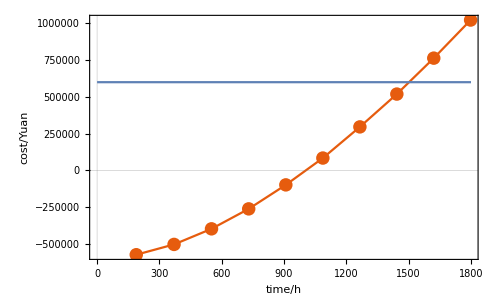

```mathematica
Show[ListLinePlot[Data1,PlotTheme->"Scientific",FrameLabel->{"time/h","cost/Yuan"},Mesh->All],Plot[600000,{x,0,1800}]]
```

### 获取数据插值函数

```mathematica
ip=Interpolation[Data1];
```

### 估计回本时间并进行可行性分析

#### 估计回本时间

```mathematica
x/.FindRoot[ip[x]==0,{x,1000}][[1]]
```

1007.89

运行1000小时时，△c（是一台装卸机和两台装卸机两种情况下 的经营费用之差）等于0。

此时对应的港口连续招待货船50到60只之间。

#### 可行性分析

我们以港口连续招待货船60只时为例，对方案两只装卸机进行100000次模拟，对应对时间分布

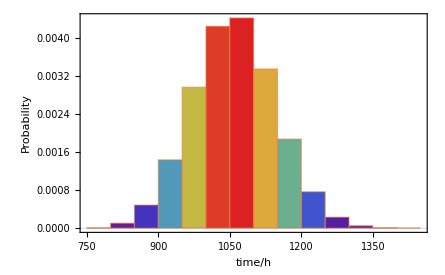

```mathematica
Histogram[Data[[6]][[1]][[All,1]],Automatic,"PDF",PlotTheme->"Scientific",FrameLabel->{"time/h","Probability"},ColorFunction->Function[{height},ColorData["Rainbow"][height]]]
```

估计其正态分布

```mathematica
EstimatedDistribution[Data[[6]][[1]][[All,1]],NormalDistribution[α,β]]
```

NormalDistribution[1058.49,85.9425]

画其图像

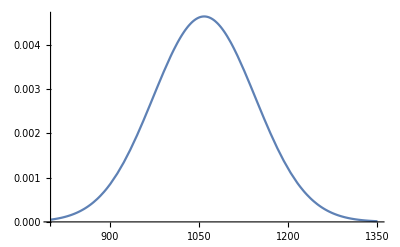

```mathematica
Plot[PDF[NormalDistribution[1058.49028,85.9424953414875]][x],{x,800,1350}]
```

重叠显示正态分布的概率密度函数曲线：

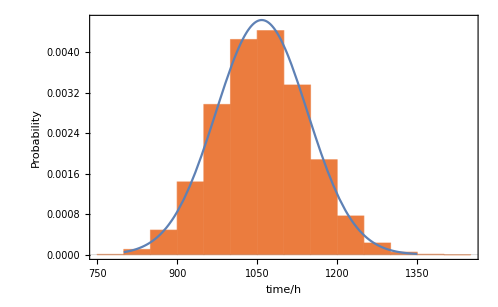

```mathematica
Show[Histogram[Data[[6]][[1]][[All,1]],Automatic,"PDF",PlotTheme->"Scientific",FrameLabel->{"time/h","Probability"}],Plot[PDF[NormalDistribution[1058.49028,85.9424953414875]][x],{x,800,1350}]]
```

同理我们可以获得一只装卸机时的情形

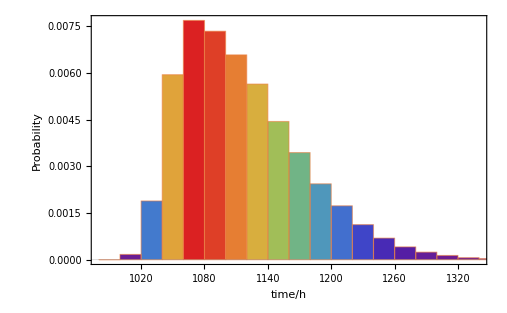

```mathematica
Histogram[Data[[6]][[2]][[All,1]],Automatic,"PDF",PlotTheme->"Scientific",FrameLabel->{"time/h","Probability"},ColorFunction->Function[{height},ColorData["Rainbow"][height]]]
```

估计其正态分布

```mathematica
EstimatedDistribution[Data[[6]][[2]][[All,1]],NormalDistribution[α,β]]
```

NormalDistribution[1115.16,57.0608]

可见平均值和方差差别不大，重叠显示正态分布的概率密度函数曲线：

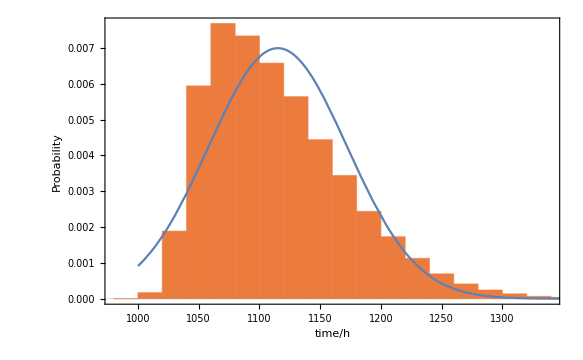

```mathematica
Show[Histogram[Data[[6]][[2]][[All,1]],Automatic,"PDF",PlotTheme->"Scientific",FrameLabel->{"time/h","Probability"}],Plot[PDF[NormalDistribution[1115.15828,57.06076486905516]][x],{x,1000,1500}]]
```

对方案两只装卸机进行100000次模拟，可视化成本分布

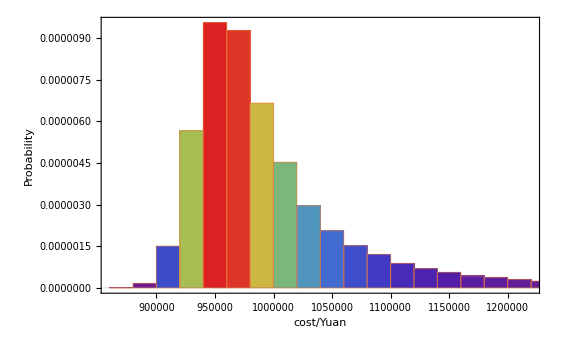

```mathematica
Histogram[Data[[6]][[1]][[All,2]],Automatic,"PDF",PlotTheme->"Scientific",FrameLabel->{"cost/Yuan","Probability"},ColorFunction->Function[{height},ColorData["Rainbow"][height]]]
```

求拟合分布

```mathematica
FindDistribution[Data[[6]][[1]][[All,2]]]
```

FindDistribution::conenf: The data will be treated as continuous. Use the option TargetFunctions->Discrete otherwise.

MixtureDistribution[{0.891985,0.108015},{LogNormalDistribution[13.7956,0.0461332],LogNormalDistribution[14.0148,0.190781]}]

重叠显示正态分布的概率密度函数曲线：

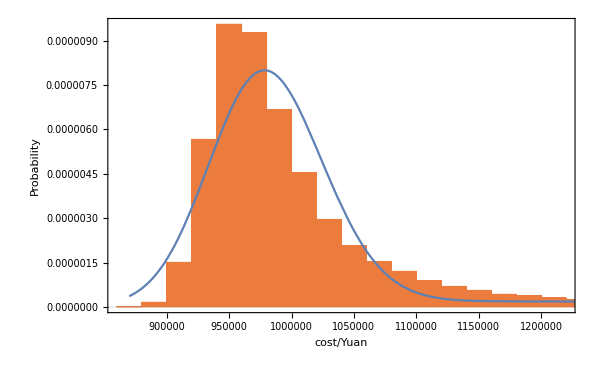

```mathematica
Show[{Histogram[Data[[6]][[1]][[All,2]],Automatic,"PDF",PlotTheme->"Scientific",FrameLabel->{"cost/Yuan","Probability"}],Plot[PDF[MixtureDistribution[{0.8919845952190129,0.10801540478098695},{LogNormalDistribution[13.795634477616293,0.04613323468705192],LogNormalDistribution[14.014810958536899,0.19078143087696917]}]][x],{x,870000,1300000}]}]
```

对方案一只只装卸机进行100000次模拟，可视化成本分布

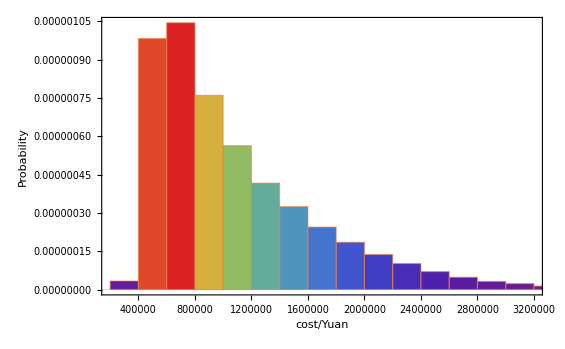

```mathematica
Histogram[Data[[6]][[2]][[All,2]],Automatic,"PDF",PlotTheme->"Scientific",FrameLabel->{"cost/Yuan","Probability"},ColorFunction->Function[{height},ColorData["Rainbow"][height]]]
```

求拟合分布

```mathematica
FindDistribution[Data[[6]][[2]][[All,2]]]
```

FindDistribution::conenf: The data will be treated as continuous. Use the option TargetFunctions->Discrete otherwise.

MixtureDistribution[{0.720961,0.279039},{LogNormalDistribution[13.6034,0.360461],LogNormalDistribution[14.4468,0.269255]}]

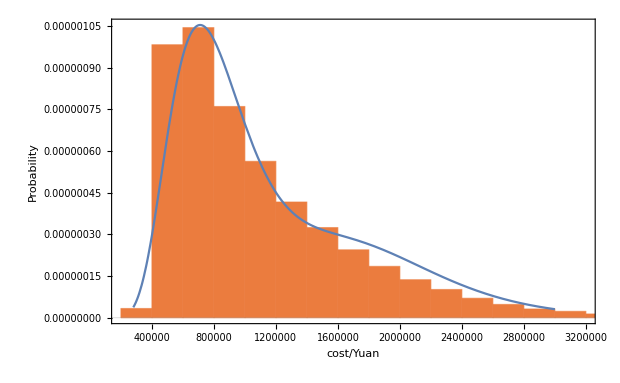

```mathematica
Show[{Histogram[Data[[6]][[2]][[All,2]],Automatic,"PDF",PlotTheme->"Scientific",FrameLabel->{"cost/Yuan","Probability"}],Plot[PDF[MixtureDistribution[{0.7209614977527261,0.2790385022472739},{LogNormalDistribution[13.603365411560175,0.3604605555021722],LogNormalDistribution[14.446771389355122,0.26925464725392445]}]][x],{x,280000,3000000}]}]
```

我们如此估计的结果是可行的

### 估计当投资回收期小于1所需要的时间并进行可行性分析

```mathematica
x/.FindRoot[ip[x]==6*10^5,{x,1000}]
```

1503.27

运行1503小时时，△c（是一台装卸机和两台装卸机两种情况下 的经营费用之差）小于1。

此时对应的港口连续招待货船80只左右。

我们看此时的成本分布

对方案两只装卸机进行100000次模拟，可视化成本分布

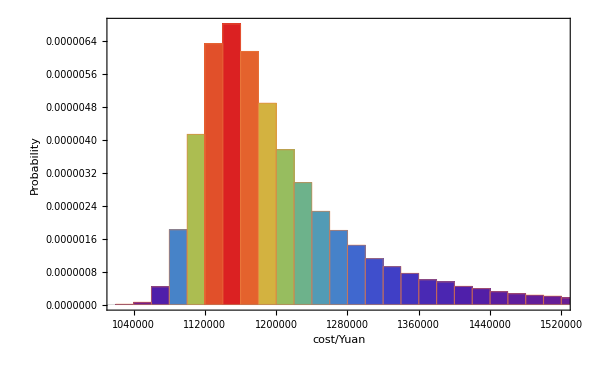

```mathematica
Histogram[Data[[9]][[1]][[All,2]],Automatic,"PDF",PlotTheme->"Scientific",FrameLabel->{"cost/Yuan","Probability"},ColorFunction->Function[{height},ColorData["Rainbow"][height]]]
```

求拟合分布

```mathematica
FindDistribution[Data[[9]][[1]][[All,2]]]
```

FindDistribution::conenf: The data will be treated as continuous. Use the option TargetFunctions->Discrete otherwise.

MixtureDistribution[{0.892666,0.107334},{NormalDistribution[1.18329×10^6,64386.3],NormalDistribution[1.51662×10^6,411721.]}]

重叠显示正态分布的概率密度函数曲线：

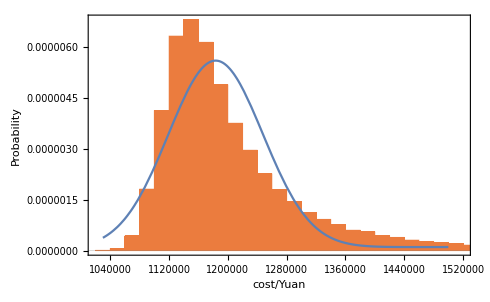

```mathematica
Show[{Histogram[Data[[9]][[1]][[All,2]],Automatic,"PDF",PlotTheme->"Scientific",FrameLabel->{"cost/Yuan","Probability"}],Plot[PDF[MixtureDistribution[{0.8926664925592596,0.10733350744074058},{NormalDistribution[1.183286353832795*^6,64386.25129642292],NormalDistribution[1.516624470764054*^6,411720.86360536376]}]][x],{x,1.03*10^6,1.5*10^6}]}]
```

对方案一只装卸机进行100000次模拟，可视化成本分布

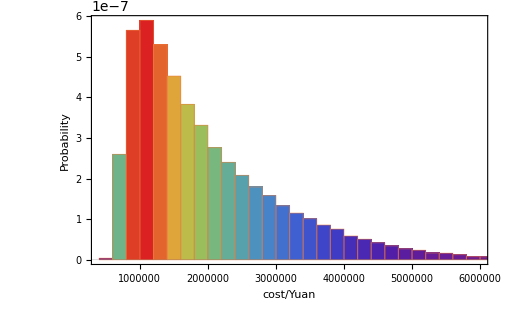

```mathematica
Histogram[Data[[9]][[2]][[All,2]],Automatic,"PDF",PlotTheme->"Scientific",FrameLabel->{"cost/Yuan","Probability"},ColorFunction->Function[{height},ColorData["Rainbow"][height]]]
```

求拟合分布

```mathematica
FindDistribution[Data[[9]][[2]][[All,2]]]
```

FindDistribution::conenf: The data will be treated as continuous. Use the option TargetFunctions->Discrete otherwise.

MixtureDistribution[{0.733205,0.266795},{LogNormalDistribution[14.1569,0.39153],GammaDistribution[6.14463,583933.]}]

重叠显示正态分布的概率密度函数曲线：

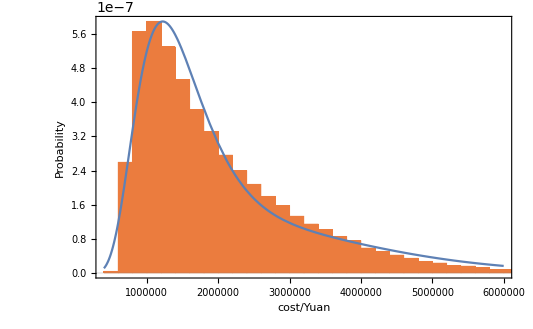

```mathematica
Show[{Histogram[Data[[9]][[2]][[All,2]],Automatic,"PDF",PlotTheme->"Scientific",FrameLabel->{"cost/Yuan","Probability"}],Plot[PDF[MixtureDistribution[{0.7332054999175431,0.26679450008245686},{LogNormalDistribution[14.15685622011754,0.39152959502142715],GammaDistribution[6.144632925275263,583932.6329735762]}]][x],{x,0.4*10^6,6*10^6}]}]
```

### C语言代码

[GitHub Code](https://github.com/yangyongkang2000/MathematicalModel/blob/master/计算机模拟/ComputerSimulation.c)

## 订货策略问题

### 问题背景：

某自行车商店的仓库管理人员采取一种简 单的订货策略, 当库存降低到P辆自行车时就向 厂家订货Q辆, 如果某一天的需求量超过了库存 量, 商店就有销售损失和信誉损失, 但如果库存 量过多, 将会导致资金积压和保管费增加. 若现 在已有如表8.2中的五种库存策略。试比较选择 一种策略以使花费最少. 已知该问题的条件  
1
2
3
4
125
125
150
175
150
250
250
250
方案编号 重新订货量P 辆 重新订货量Q 辆
5 175 300
已知该问题的条件:
1) 从发出订货到收到货物需隔3天;
2) 每辆自行车保管费为0.75元/天,每辆自行车的缺
货损失为1.80元/天,每次的订货费为75元; 3)每天自行车的需求量服从0到99之间的均匀分布; 4)原始库存为115辆,并假设第一天没有发出订货.
 试比较选择一种策略以使得花费最少.

### Wolfram+C语言编程模拟

```mathematica
function1[P_Integer,Q_Integer,m_Integer,n_Integer,file_String]:=Run["/Users/yangyongkang/Desktop/b.out calc "<>StringRiffle[(ToString/@{P,Q,m,n})~Append~("./Data/"<>file),"-"]]
```

```mathematica
Module[{t=1},function1[#1,#2,365,100000,ToString[t++]<>".wl"]&@@@{{125,150},{125,250},{150,250},{175,250},{175,300}}]
```

{0,0,0,0,0}

```mathematica
CostList=Table[Get["./Data/"<>ToString[n]<>".wl"],{n,1,5}];
```

### 模拟数据可视化展示

对五种策略，进行365天范围内的成本分析，每个分析模拟100000次。

绘制五个策略成本数据集 data_i 的直方图.

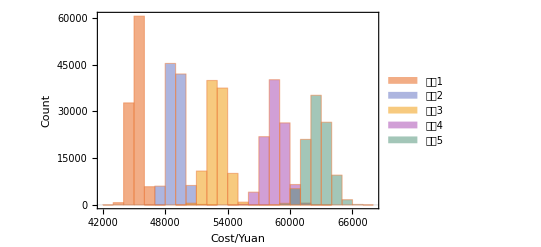

```mathematica
Histogram[CostList,ChartLegends->("策略"<>ToString[#]&/@Range[5]),PlotTheme->"Scientific",FrameLabel->{"Cost/Yuan","Count"}]
```

### 五种策略的概率分布直方图

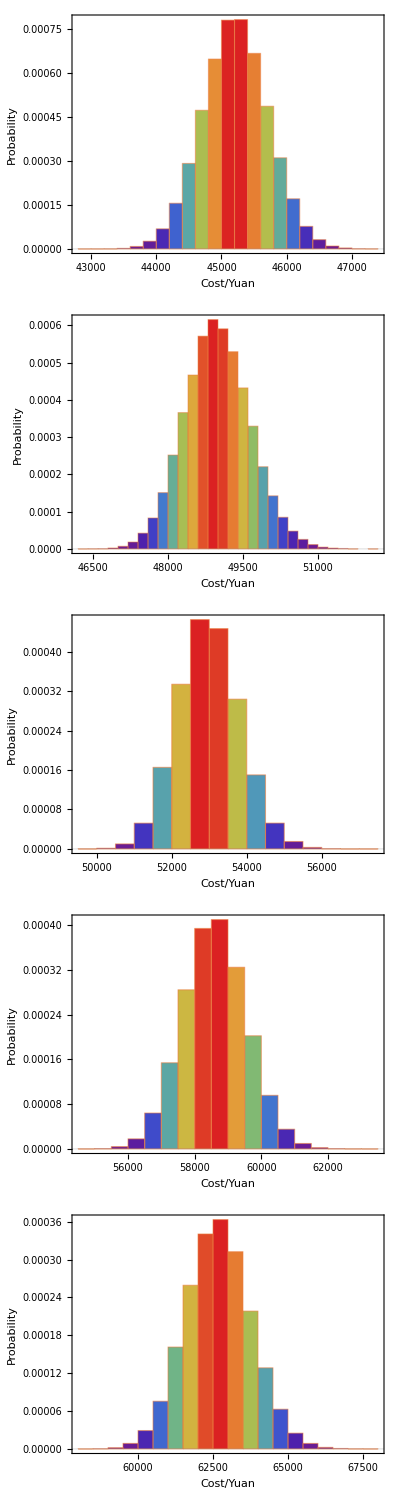

```mathematica
Table[Histogram[CostList[[i]],Automatic,"PDF",ColorFunction->Function[{height},ColorData["Rainbow"][height]],PlotTheme->"Scientific",FrameLabel->{"Cost/Yuan","Probability"}],{i,1,5}]//Column
```

可以分析出来，方案一最节省成本。

### C语言代码

[GitHub Code](https://github.com/yangyongkang2000/MathematicalModel/blob/master/计算机模拟/ComputerSimulation1.c)

## 等公交车问题

### 题目背景：

某公共汽车站每隔30分钟到达一辆汽车，但可能有[0,3] 分钟的误差，此误差大小与前一辆汽车的运行无关。汽 车最多容纳50名旅客，到达该汽车站时车内旅客人数服 从[20，50]的均匀分布。到站下车的旅客人数服从[3，7] 的均匀分布，每名旅客下车的时间服从[1，7]秒的均匀 分布。旅客按每30分钟到达12个人的泊松分布到达汽车 站，单列排队等车，先到先上，如果某位旅客未能上车， 他将不再等候。旅客上车时间服从[4，12]秒的均匀分布。 上下车的规则是:先下后上，逐个上车，逐个下车。 假设每天共发25辆汽车，现在要求模拟一天汽车的运 行情况，了解一天中在站内等候汽车的总人数、能上 车及不能上车的人数、旅客排队时间分布情况、不能 上 车人数的分布情况等。

### 条件假设：

假设每个乘客到达汽车站的时间间隔遵循指数分布，根据题意（旅客按每30分钟到达12个人的泊松分布到达汽车 站，单列排队等车），参数为150.我们对指数分布得到的时间分布取整，时间单位精确到s.

### Wolfram+C语言模拟

```mathematica
function2[n_Integer,file1_String,file2_String]:=Run["./Desktop/c.out "<>"calc "<>ToString[n]<>" ./Data/"<>file1<>" ./Data/"<>file2]
```

### 模拟结果

计算机模拟10000天情况

```mathematica
function2[10000,"dataset1.wl","dataset2.wl"]
```

0

#### 旅客排队时间分布情况

时间概率分布直方图

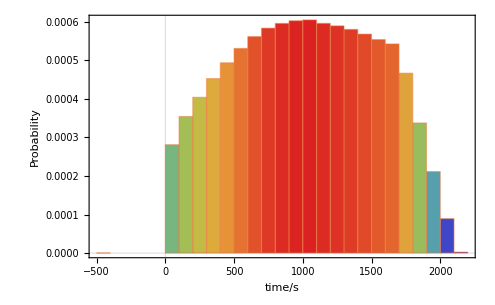

```mathematica
Histogram[data=Get["./Data/dataset1.wl"],Automatic,"PDF",ColorFunction->Function[{height},ColorData["Rainbow"][height]],PlotTheme->"Scientific",FrameLabel->{"time/s","Probability"}]
```

时间概率分布平滑核直方图

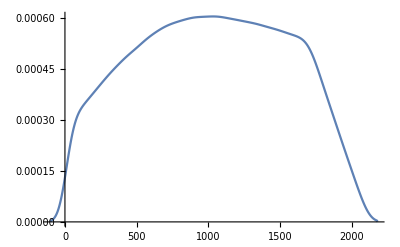

```mathematica
SmoothHistogram[data,Automatic,"PDF"]
```

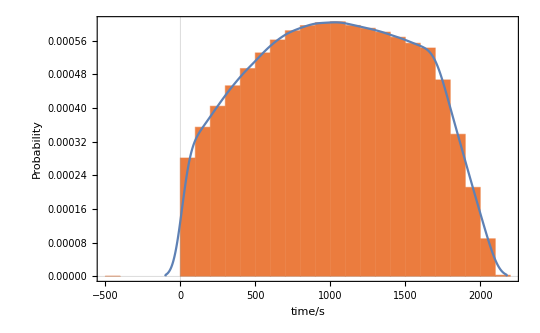

```mathematica
Show[Histogram[data,Automatic,"PDF",PlotTheme->"Scientific",FrameLabel->{"time/s","Probability"}],SmoothHistogram[data,Automatic,"PDF"]]
```

旅客排队时间数据的平均值，标准差。

平均值

```mathematica
Mean@data//N
```

1017.33

标准差

```mathematica
StandardDeviation@data//N
```

522.445

#### 等候汽车的总人数、能上 车及不能上车的人数分布情况

```mathematica
data1=Get["./Data/dataset2.wl"];
```

等候汽车的总人数分布直方图

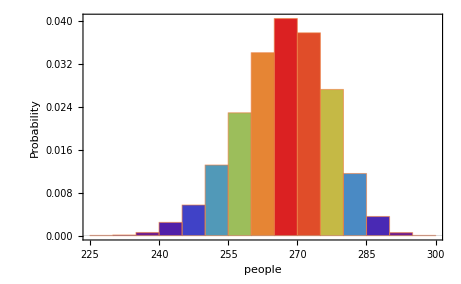

```mathematica
Histogram[data1[[1]],Automatic,"PDF",ColorFunction->Function[{height},ColorData["Rainbow"][height]],PlotTheme->"Scientific",FrameLabel->{"people","Probability"}]
```

等候汽车人数数据的平均值，标准差。

平均值

```mathematica
Mean[data1[[1]]]//N
```

266.633

标准差

```mathematica
StandardDeviation[data1[[1]]]//N
```

9.57486

能上车人数分布直方图

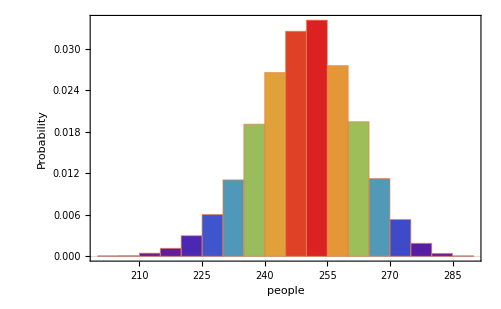

```mathematica
Histogram[data1[[2]],Automatic,"PDF",ColorFunction->Function[{height},ColorData["Rainbow"][height]],PlotTheme->"Scientific",FrameLabel->{"people","Probability"}]
```

能上车人数数据的平均值，标准差。

平均值

```mathematica
Mean@data1[[2]]//N
```

249.131

标准差

```mathematica
StandardDeviation[data1[[2]]]//N
```

11.8422

不能上车人数分布直方图

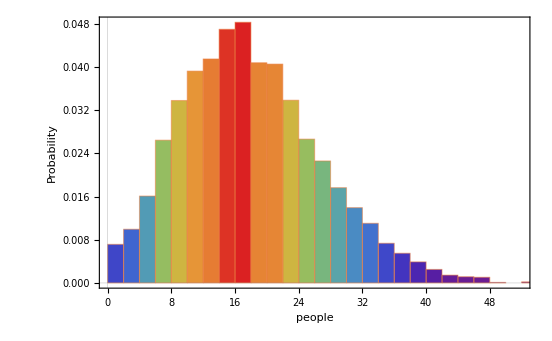

```mathematica
Histogram[data1[[3]],Automatic,"PDF",ColorFunction->Function[{height},ColorData["Rainbow"][height]],PlotTheme->"Scientific",FrameLabel->{"people","Probability"}]
```

估计分布

```mathematica
FindDistribution[data1[[3]]]
```

MixtureDistribution[{0.200857,0.799143},{DiscreteUniformDistribution[{0,18}],NegativeBinomialDistribution[8,0.283444]}]

平滑核分布直方图

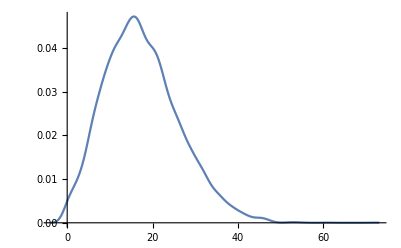

```mathematica
SmoothHistogram[data1[[3]],Automatic,"PDF"]
```

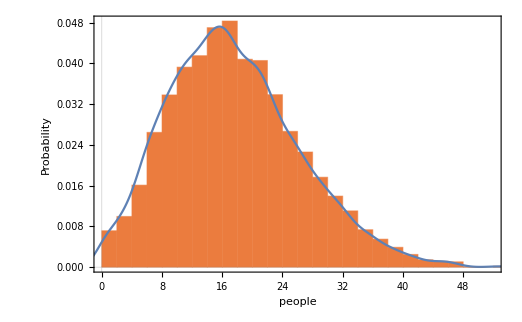

```mathematica
Show[Histogram[data1[[3]],Automatic,"PDF",PlotTheme->"Scientific",FrameLabel->{"people","Probability"}],SmoothHistogram[data1[[3]],Automatic,"PDF"]]
```

能上车人数数据的平均值，标准差。

平均值

```mathematica
Mean@data1[[3]]//N
```

17.5018

标准方差

```mathematica
StandardDeviation@data1[[3]]//N
```

8.7424

### C语言代码

[GitHub Code](https://github.com/yangyongkang2000/MathematicalModel/blob/master/计算机模拟/ComputerSimulation2.c)

## 港口停靠问题

### 题目背景：

"某港口提供有足够的泊位供船舶停靠，但现在仅有一个 可供装卸的泊位，船舶先到则先进行装卸，
如果船舶得 不到及时装卸而造成的滞期费为每小时100元。
现要弄 清该系统的性能，
重点考察船舶进入该港后等待装卸的 滞留时间以及卸位(即装卸用的泊位)的利用率，从而 进行经济效益分析。
 首先，对进入该港口的100艘船进行实际调查，记录其活动情况， 
 得到这100艘船到达港口的时间间隔和装卸时间的分布情况的频 数和累积频率分布。
设:一年内到达港口的船舶数为N，到港船舶滞留总时间 为T1，
  船舶平均滞留时间为T2，港口支付滞留费为Y，装 卸泊位空闲时间装卸泊位利用率S。
Step1: 模拟船舶到达港口的时间间隔的分布P1， Step2: 模拟船舶装卸所需时间的分布P2， Setp3: 编写程序。
   为了比较准确地反映系统的性能，我们采用稳态模拟 方式，可以考察系统运行360天的情况。假定港口每 天24小时连续工作，因此模拟时间T设置为8640小时。 考虑到船舶到达港口的事件是影 响整个系统状态的 主要因素，可以将模拟事件设置为该事件的发生时刻。
   所用变量说明:
• t:一艘船到达港口的时间;
• tl:前一艘船驶离港口的时间;
• td:两艘船到达港口的时间间隔;
• ts:当前船舶装卸所需时间;
• tw:t时刻所有已到达港口的船舶等待装卸时间总和;
• tf:t时刻装卸位已空闲时间总和;
   经过6次模拟计算，装卸泊位的平均利用率为95.3%， 
   但到达的船舶的却因得不到及时的服务而造成平均每 艘滞留9.295小时，
   每年到港船舶总滞留6843小时， 因此港口每年约需支付68万元的滞留费，
   这显然是一 笔不小的开支。为此，可修改模拟模型，考虑增设一 个装卸泊位，并重新进行模拟运行，
   将这些数据提供 给决策者一确定是否需要再新建一个装卸泊位。"

### Wolfram+C编程模拟

规定滞期为货船停靠到装卸完毕花费的总时间，C语言源码网址：["Ubuntu Code"](https://paste.ubuntu.com/p/spyFySsPyR/)

对一年进行100000万次模拟，对数据进行可视化

#### 一年招待的货船概率直方图

```mathematica
data3=Get["/home/yang/文档/ComputerSimulation/a.wl"];
```

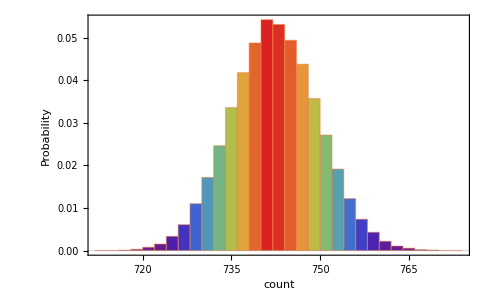

```mathematica
Histogram[data3[[2]],Automatic,"PDF",ColorFunction->Function[{height},ColorData["Rainbow"][height]],PlotTheme->"Scientific",FrameLabel->{"count","Probability"}]
```

港口年招待的货船数量与总滞期的时间比值概率分布直方图

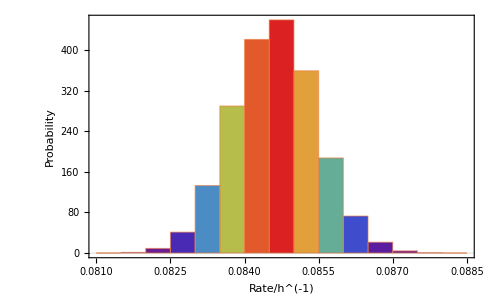

```mathematica
Histogram[data3[[2]]~Divide~data3[[1]],Automatic,"PDF",ColorFunction->Function[{height},ColorData["Rainbow"][height]],PlotTheme->"Scientific",FrameLabel->{"Rate/h^(-1)","Probability"}]
```

#### 港口支付滞期费用概率分布直方图

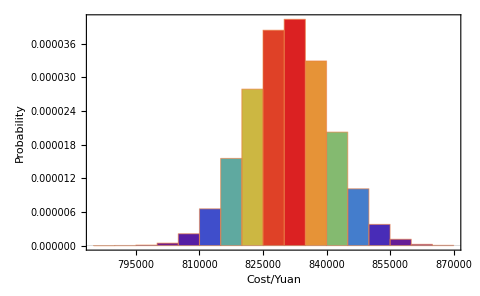

```mathematica
Histogram[data3[[3]],Automatic,"PDF",ColorFunction->Function[{height},ColorData["Rainbow"][height]],PlotTheme->"Scientific",FrameLabel->{"Cost/Yuan","Probability"}]
```

每只船只平均滞期费用概率分布直方图

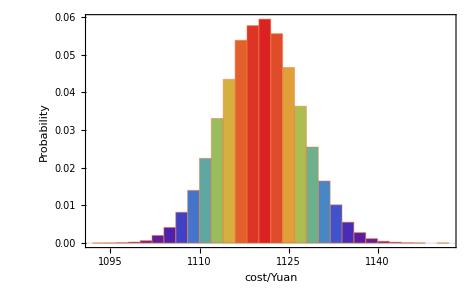

```mathematica
Histogram[data3[[3]]~Divide~data3[[2]],Automatic,"PDF",ColorFunction->Function[{height},ColorData["Rainbow"][height]],PlotTheme->"Scientific",FrameLabel->{"cost/Yuan","Probability"}]
```

#### 每只船只平均滞期时间概率分布直方图

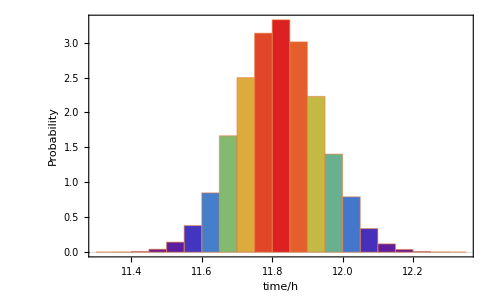

```mathematica
Histogram[data3[[1]]~Divide~data3[[2]],Automatic,"PDF",ColorFunction->Function[{height},ColorData["Rainbow"][height]],PlotTheme->"Scientific",FrameLabel->{"time/h","Probability"}]
```

#### 与一个装载泊位对比

-Graphics-

发现两个装载泊位比一个装载泊位效率低。